# Estadística

## Distribución binomial

Es una distribución de probabilidad discreta que describe la probabilidad de un número sucesivo de eventos en un experimento donde el resultado es binario (éxito o fracaso), donde la probabilidad de éxito está dada por p, y la probabilidad de fracaso es q = 1-p. Su función de probabilidad es

f(k, n, p) = (n
k) p^k (1-p)^(n-k),
donde n es el número de intentos, y k es el número de éxitos.
El valor esperado es

E(X) = nP,

y la varianza

V(X) = E(X^2) = nPQ.

Ejemplo

Se hace un experimento en el cual se hace 100 tiros sucesivos de una moneda y se mide el número de veces que sale una cierta cara. El número de intentos es n=100, la probabilidad de éxito es p = 0.5. Si se grafica la probabilidad de obtener cada número de exitos se obtiene una distribución como la que se muestra.

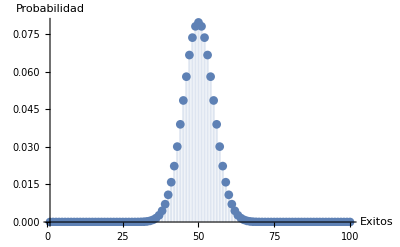

```mathematica
DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,100},PlotRange->All,PlotMarkers->Automatic, AxesLabel->{"Exitos", "Probabilidad"}]
```

## Teorema del límite central

La media aritmética de la suma de un gran número de variables aleatorias independientes se distribuye aproximadamente en una distribución normal sin importar sus distribuciones individuales.

```mathematica
(* Fuente: http://www.demonstrations.wolfram.com/TheCentralLimitTheorem/ *)
Manipulate[SeedRandom[seed];
Show[Histogram[Table[Mean[RandomReal[{0,100},n]],{200}],{35,65,1}],Plot[200*PDF[NormalDistribution[50,Sqrt[9999/(12 n)]],x],{x,35,65}],ImageSize->{500,300}],{{n,20,"Tamaño de la muestra"},10,200,1,Appearance->"Labeled"},{{seed,1,"Semilla"},1,100000,1}]
```

## Distribución normal

La importancia de esta distribución radica en que permite modelar numerosos fenómenos naturales, sociales y psicológicos. Mientras que los mecanismos que subyacen a gran parte de este tipo de fenómenos son desconocidos, por la enorme cantidad de variables incontrolables que en ellos intervienen, el uso del modelo normal puede justificarse asumiendo que cada observación se obtiene como la suma de unas pocas causas independientes (Fuente: Wikipedia). Su función de densidad de probabilidad es
f(x) = 1/(σ √(2 π))e^(-(x-μ)^2/(2 σ^2)).

Ejemplo

El coeficiente intelectual se distribuye aproximadamente de forma normal con media 100 y desviación estándar 16. ¿Cuál es la probabilidad de que un individuo tenga un IQ a) menor a 90, b) mayor a 130 y c) entre 95 y 105?

```mathematica
μ = 100;
σ = 16;
Print["a) " <>ToString[100*N[∫_(-∞)^90 PDF[NormalDistribution[μ,σ],x]ⅆx]] <> " %"]
Print["b) " <>ToString[100*N[∫_130^∞ PDF[NormalDistribution[μ,σ],x]ⅆx]] <> " %"]
Print["c) " <>ToString[100*N[∫_95^105 PDF[NormalDistribution[μ,σ],x]ⅆx]] <> " %"]
```

a) 26.5986 %

b) 3.03964 %

c) 24.5339 %

a) ¿Cuál es la probabilidad que la media del IQ de un grupo de 12 personas escogido aleatoriamente esté entre 95 y 105? b) ¿Qué tan grande debe ser la muestra para tener una probabilidad de 95 % de que la media del IQ esté entre estos límites?

Supongamos que se hace una serie de n observaciones, x_1, x_2,...,x_n , sobre una variable aleatoria y se calcula su media x̄, se se realiza otra serie de n onservaciones  x'_1, x'_2,...,x'_n  y se calcula su media x̄', si se sigue el procedimiendo sucesivamente se obtendrá una distribución de las medias. A esta distribución se le conoce como distribución de muestreo. Para averiguar cómo son los valores de expectación de esta distribución se hace

E(n x̄) = E(x_1+ x_2+...+x_n ) = E(x_1) + E(x_2) + ... + E(x_n)  = n μ,
V(n x̄) = V(x_1+ x_2+...+x_n ) = V(x_1) + V(x_2) + ... + V(x_n)  = n σ^2.

Con esto se puede calcular E y V sobre x̄.

E(x̄) = E((n x̄)/n) = (E(n x̄))/n = μ,
V(x̄) = V((n x̄)/n) = (V(n x̄))/n^2 = σ^2/n.

La distribución de la muestra es una distribución normal con media μ y varianza σ^2/n. Entonces

```mathematica
μ = 100;
σ = 16;
n = 12;
Print["a) " <>ToString[100*N[∫_95^105 PDF[NormalDistribution[μ,√(σ^2/n)],x]ⅆx]] <> " %"]
Clear[n];
Off[Solve::ifun];
Print["b) n = " <>ToString[Ceiling[n /. Solve[∫_95^105 PDF[NormalDistribution[μ,√(σ^2/n)],x]ⅆx == 0.95,n][[1]]]]]
```

a) 72.0984 %

b) n = 40

Se puede obtener una aproximación numérica a esta solución generando la distribución de las medias e integrando de 95 a 105.

```mathematica
Manipulate[
SeedRandom[seed];
μ =100;
σ = 16;
n = 12; (* Tamaño de la muestra *)
dist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
m = Mean[sample];
AppendTo[dist,m];,
{k}
];
Show[
Histogram[dist,20,"ProbabilityDensity",PlotLabel->"P = " <> ToString[100*Integrate[PDF[HistogramDistribution[dist],x],{x,95,105}]]<> " %"],
Plot[Evaluate[PDF[NormalDistribution[μ,√(σ^2/n)],x]],{x,0,200},PlotRange->Full]
]
,
{{k,100},1,2450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

## Distribución χ^2

La distribución χ^2 con k grados de libertad es la distribución de la suma de los cuadrados de k variables normales independientes Y = Z_1^2+Z_2^2+ ... + Z_k^2, donde cada Z es independiente y está normalmente distribuido con media cero y varianza uno. La distribución χ^2 se puede interpretar como la distribución del cuadrado de la desviación estándar en una muestra. En concreto (n-1) S^2/σ^2 sigue la distribución χ^2.

```mathematica
Manipulate[
SeedRandom[seed];
data= RandomVariate[NormalDistribution[0,1],10^4]^2;
Do[
data += RandomVariate[NormalDistribution[0,1],10^4]^2;,
{k-1}
];
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[Evaluate[PDF[ChiSquareDistribution[k],x]],{x,0,100},PlotRange->Full]
],
{{k,2},1,50,1,Appearance->"Labeled"},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

Ejemplo

El coficiente intelectual es aproximadamente normalmente distribuido con μ=100, y σ = 16. En un grupo de 10 individuos seleccionados aleatoriamente, ¿cuál es la probabilidad de que la desviación estándar observada ‘s’ sea menor a 8.8?

En una muestra con n grados de libertad la distribución de su varianza está relacionada con la distribución χ^2, (n-1) S^2/σ^2 sigue la distribución χ^2. Sea f(x) la función de densidad de la distribución χ^2, con esto se puede obtener la probabilidad de que la desviación estándar sea menor a 8.8 integrando con los límites x_i = 0, x_f = (n-1) 8.8/σ^2, de manera que ∫_x_i^x_f f(x) dx = 0.0257108. A continuación se hará la prueba generando la distribución (n-1) S^2/σ^2 y comparando con la distribución χ^2.

```mathematica
Manipulate[
SeedRandom[seed];
μ =100;
σ = 16;
n = 10; (* Tamaño de la muestra *)
dist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
s = (n-1) StandardDeviation[sample]^2 / σ^2;
AppendTo[dist,s];,
{k}
];
Show[
Histogram[dist,20,"ProbabilityDensity"],
Plot[Evaluate[PDF[ChiSquareDistribution[n-1],x]],{x,0,100},PlotRange->Full]
]
,
{{k,1500},1,4450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
Print["La probabilidad es: "];
100*Integrate[PDF[ChiSquareDistribution[n-1],x],{x,0,(n-1)(8.8/σ)^2}]
```

La probabilidad es:

2.57108

Una manera alternativa de obtener este resultado es generando una distribución de desviaciones estándar a través de k muestras e integrar sobre la distribución del histograma.

```mathematica
Manipulate[
SeedRandom[seed];
μ =100;
σ = 16;
n = 10; (* Tamaño de la muestra *)
dist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
s =  StandardDeviation[sample];
AppendTo[dist,s];,
{k}
];
Show[
Histogram[dist,20,"ProbabilityDensity", PlotLabel->"P = " <> ToString[100*Integrate[PDF[HistogramDistribution[dist],x],{x,0,8.8}]]<> " %"],
Plot[Evaluate[PDF[HistogramDistribution[dist],x]],{x,0,8.8},PlotRange->Full,Filling->Axis, FillingStyle->Blue]
]
,
{{k,1500},1,4450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

## Distribución t-Student

La distribución t de Student se usa para estimar parámetros cuando el tamaño de la muestra es muy pequeña. Esta distribución se define como

T = Z/(√(Y/k)).  Entonces cada medición está dada por t = (x̄- μ)/(s/√n), donde s = 1/(n-1)∑_(i=1)^N (x_i- x̄)^2. La distribución t-Student se puede interpretar como la distribución de la localización de la media verdadera.
En esta prueba se observa cómo la muestra generada a partir de la definición T = Z/(√(Y/k)) se ajusta a la distribución de Student.

```mathematica
Manipulate[
SeedRandom[seed];
data=RandomVariate[NormalDistribution[0,1],10^4]/√(RandomVariate[ChiSquareDistribution[k],10^4]/k);
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[StudentTDistribution[k],x],{x,-9,9},PlotStyle->Thick, PlotRange->Full]],
{{k,2},1,50},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

Otra prueba es generar valores a partir de t = (x̄- μ)/(s/√n), donde x̄ se genera a partir de una distribución normal, y μ y σ se generan aleatoriamente.

```mathematica
Manipulate[
SeedRandom[seed];
μ = RandomInteger[100];
σ = RandomInteger[100];
n = 10^4; (* Tamaño de la muestra *)
tDist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
s = StandardDeviation[sample];
t = (Mean[sample]-μ)/(s/√n);
AppendTo[tDist,t];,
{k}
];
Show[
Histogram[tDist,20,"ProbabilityDensity"],
Plot[PDF[StudentTDistribution[k],x],{x,-100,100},PlotStyle->Thick, PlotRange->Full]
]
,
{{k,50},1,450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

Ejemplo

Si se realizan 4 observaciones de una distribución normal, ¿cuál es la probabilidad de que la diferencia entre la media observada x̄ y la media verdadera μ sea menor a cinco veces la desviación estándar observada s?

La distribución t-Student nos da una medida de cuánto se aleja la media de la medición de la media real respecto a la varianza de la medición (x̄- μ)/(s/√n). Lo que se busca entonces es ver cuál es el porcentaje de valores de la distribución t-Student que está entre -5 y 5. Esto se puede hacer integrando la función de densidad de la distribución f(x), de manera que ∫_-5^5 f(x) dx = 0.99251.

A continuación se compara el cálculo analítico con una aproximación numérica.

```mathematica
Manipulate[
SeedRandom[seed];
μ =0;
σ = 1;
n = 4; (* Tamaño de la muestra *)
dist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
s = (Mean[sample]-μ)/(5 StandardDeviation[sample]);
AppendTo[dist,s];,
{k}
];
Show[
Histogram[dist,50,"ProbabilityDensity", PlotLabel->"P = " <> ToString[100*Integrate[PDF[HistogramDistribution[dist],x],{x,-1,1}]] <> " %"],
Plot[Evaluate[PDF[HistogramDistribution[dist,50],x]],{x,-1,1},PlotRange->Full,Filling->Axis, FillingStyle->Blue]
]
,
{{k,1500},1,4450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]

Print["El cálculo analítico arroja: "];
N[100Integrate[PDF[StudentTDistribution[4],x],{x,-5,5}]]
```

El cálculo analítico arroja:

99.251

## Pruebas de significancia

Distribución binomial

Cuando se quiso describir la probabilidad de obtener la proporción en el número de veces que sale cierto lado de una moneda se utilizó una distribución binomial. Si ahora se repite el experimento y se obtiene X número de caras y Y número de cruces, para determinar si este resultado está de acuerdo con la distribución que se cree que la genera se utiliza una prueba de significancia. Para realizar la prueba de significancia se escoge un p-valor que es la probabilidad de obtener un resultado al menos tan extremo como el que se ha obtenido. Si la probabilidad de obtener la muestra es menor que el p-valor escogido se rechaza la hipótesis de que la muestra pertenece a la distribución.

En el caso de la moneda si se escoge un p-valor de 5 % para determinar a partir de qué proporción de X y Y se considera que el resultado no pertenece a la distribución hay que fijarse en la función de densidad cumulativa. El p-valor debe corresponder a la probabilidad de obtener todos los valores extremos, que son los valores sombreados en la siguiente gráfica.

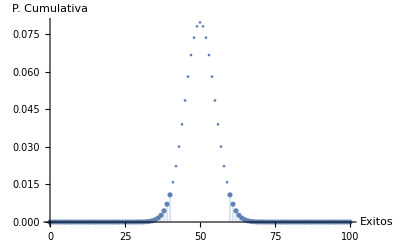

```mathematica
Show[
DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,0,100},PlotRange->All, AxesLabel->{"Exitos", "P. Cumulativa"},Filling->None],
DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,0,40},PlotRange->All, AxesLabel->{"Exitos", "P. Cumulativa"}],
DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,60,100},PlotRange->All, AxesLabel->{"Exitos", "P. Cumulativa"}]
]
```

Se multiplica por dos la probabilidad cumulativa debido a la simetría de la gráfica anterior.

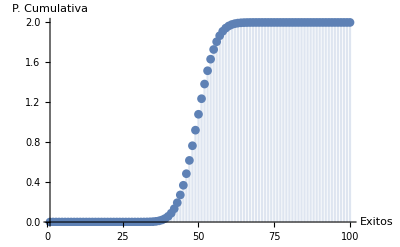

```mathematica
DiscretePlot[2*CDF[BinomialDistribution[100,0.5],k],{k,100},PlotRange->All,PlotMarkers->Automatic, AxesLabel->{"Exitos", "P. Cumulativa"}]
```

A partir de 40 éxitos la probabilidad cumulativa supera 0.05, de manera que se pueden rechazar los resultados que obtengan resultados menores a 40. De la misma manera (por simetría) se rechazan los resultados mayores a 60.

Una manera más simple de calcular el intervalo de confianza es utilizando los cuantiles de α/2 a 1-α/2.

```mathematica
Quantile[BinomialDistribution[100,0.5],{α/2,1-α/2}]
```

{40,60}

```mathematica
d[x1_,n1_,x2_,n2_]:= Module[{p1,p2,p,q},
p1 = x1/n1; p2 = x2/n2;
p = (x1+x2)/(n1+n2); q = 1-p;

Return[N[(p1-p2)/(√(p q (1/n1+1/n2)))]];
];
```

Ahora se considerará el problema de determinar si dos muestras generadas a partir de una distribución binomial comparten la misma distribución. Para ello se considera que si se tiene una muestra con probabilidad de éxito p y la hipótesis es que procede de una distribución con probabilidad P, entonces p-P estará normalmente distribuido. Entonces la resta de p_1-p_2, donde p_1 y p_2 provienen de muestras diferentes, estará también normalmente distribuida.

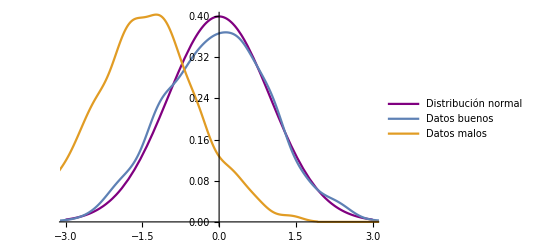

```mathematica
distBuena = {};
distMala = {};
n1 = 150;
n2 = 78;
iter = 1000;
Do[
data1 = RandomVariate[BinomialDistribution[n1,0.5]];
data2 = RandomVariate[BinomialDistribution[n2,0.5]];
data3 = RandomVariate[BinomialDistribution[n2,0.6]];
AppendTo[distBuena,d[data1,n1,data2,n2]];
AppendTo[distMala,d[data1,n1,data3,n2]];
,{iter}
]
Show[
Plot[PDF[NormalDistribution[],x],{x,-3,3}, PlotStyle->Purple,PlotLegends->{"Distribución normal"}],
SmoothHistogram[{distBuena,distMala},PlotLegends->{"Datos buenos", "Datos malos"}]
]
```

A partir de esto se puede idear una prueba para determinar si las muestras pertenecen a la misma distribución con un nivel de significancia α. Para las siguientes muesras se observa que la probabilidad de que el valor de d generado por las muestras tenga un valor mayor al obtenido.

```mathematica
n1 = 100;
data1 = RandomVariate[BinomialDistribution[n1,0.5]];
n2 = 100;
data2 = RandomVariate[BinomialDistribution[n2,0.5]];
dval = d[data1,n1,data2,n2];
Probability[x >Abs[dval] ∨ x < -Abs[dval] ,x\[Distributed]NormalDistribution[]]
```

0.479478

Para dos variables generadas por la misma distribución el valor 0.47 supera el valor de significancia α =0.05, de manera que no se puede rechazar la hipótesis de que pertenezcan a la misma distribución. Para dos variables generadas por diferentes distribuciones,

```mathematica
n1 = 100;
data1 = RandomVariate[BinomialDistribution[n1,0.7]];
n2 = 100;
data2 = RandomVariate[BinomialDistribution[n2,0.5]];
dval = d[data1,n1,data2,n2];
Probability[x >Abs[dval] ∨ x < -Abs[dval],x\[Distributed]NormalDistribution[]]
```

0.00657266

se observa que 0.006 < α=0.05, de manera que se puede rechazar la hipótesis de que fueron generadas por la misma distribución.

Distribución t-Student

Supongase que se realizan una serie de observaciones x_1, x_2, ...  ,x_n , sobre una variable aleatoria con media μ y varianza σ^2, se quiere probar que la hipótesis de que μ = μ_0. La forma natural de realizar esto es calcular la media de la muestra x̄ y ver si es aproximadamente igual a μ_0. Si se hace esto sucesivas veces se obtendrá una distribución normal con media μ_0 y varianza σ^2/(√n), de manera que

d = (x̄-μ_0)/(σ/√n)

es una variable aleatoria con distribución normal de media cero y varianza uno. A partir de esto se podría verificar la hipótesis nula, pero el problema radica en que por lo general no se conoce σ, de manera que es necesario utilizar la varianza de la muestra, de manera que 

t = (x̄-μ)/(s/√n)

es una variable aleatoria con distribución t-Student. A continuación se muestra un ejemplo de las distribuciones generadas a partir de una variable aleatoria que sí pertenece a una distribución normal igual a la hipótesis, y otra que no pertenece.

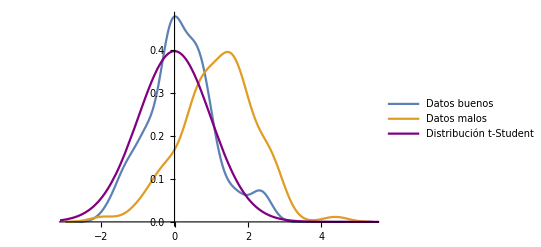

```mathematica
μ1 = 0;
μ2 = 0.01;
σ = 1;
n = 10^4; (* Tamaño de la muestra *)
tDistBuena = {};
tDistMala = {};
iter = 100;
Do[
sample1 = RandomVariate[NormalDistribution[μ1,σ],n];
s1 = StandardDeviation[sample1];
t1 = (Mean[sample1]-μ1)/(s1/√n);

sample2 = RandomVariate[NormalDistribution[μ2,σ],n];
s2 = StandardDeviation[sample2];
t2 = (Mean[sample2]-μ1)/(s2/√n);

AppendTo[tDistBuena,t1];
AppendTo[tDistMala,t2];,
{iter}
];
Show[
SmoothHistogram[{tDistBuena,tDistMala},PlotLegends->{"Datos buenos", "Datos malos"}],
Plot[PDF[StudentTDistribution[iter],x],{x,-6,6}, PlotRange->Full,PlotLegends->{"Distribución t-Student"}, PlotStyle->Purple]
]
```

También se puede utilizar esta prueba para determinar si dos variables aleatorias pertenecen a la misma distribución. Si se hacen m mediciones sobre una variable aleatoria X y n mediciones sobre Y, entonces

t = (x̄-ȳ)/(s √(1/m+1/n))
sigue una distribución de student con m+n-2 grados de libertad si μ_1 = μ_2. Si no se puede asumir que las varianzas de ambas variables aleatorias son iguales, pero en número de muestras es grande entonces se puede utilizar

t’ =  (x̄-ȳ)/(s √(S_1^2/(m(m-1))+S_2^2/(n(n-1)))), donde S_1^2= ∑_(i=1)^m (x_i-x̄)^2, y S_2^2= ∑_(i=1)^n (y_i-ȳ)^2.

De esta forma se puede hacer una prueba para verificar si las medias de dos muestras proceden de la misma distribución. Para el caso en el que las muestras se generan con la misma media no se puede rechazar la hipótesis nula.

```mathematica
StudentTestMeans[μ1_,μ2_,m_,n_]:= Module[{sample1,sample2,xM,yM,s,t},
sample1 = RandomVariate[NormalDistribution[μ1,1],m];
sample2 = RandomVariate[NormalDistribution[μ2,1],n];
xM = Mean[sample1];
yM = Mean[sample2];
s = √((Sum[(x-xM)^2,{x,sample1}]+Sum[(y-yM)^2,{y,sample2}])/(m+n-2));
t = (xM-yM)/(s √(1/m+1/n));
Return[Probability[x >Abs[t] ∨ x < -Abs[t] ,x\[Distributed]StudentTDistribution[m+n-2]]];
];

StudentTestMeans[0,0,15,10]
```

0.92081

Para el caso en el que las muestras fueron generadas con medias diferentes se rechaza fácilmente la hipótesis nula.

```mathematica
StudentTestMeans[0,1,15,10]
```

0.000756585

Prueba χ^2 de bondad de ajuste

Si se desea estimar qué tan probable es que una muestra siga una distribución específica se utiliza la prueba χ^2. En esta prueba el criterio está dado por

χ^2 = ∑_(i=1)^k (n_i-E_i)^2/E_i, donde χ^2 sigue precisamente la distribución χ^2. n_i es el número de observaciones de cierta clase, E_i el valor esperado de observaciones dado por E_i = n P_i, y k es el número total de clases.

A continuación se hará una prueba de bondad de ajuste para la distribución normal, tomando muestras generadas por una distribución normal y una distribución de student.

```mathematica
data1=RandomVariate[NormalDistribution[],10^4];
data2=RandomVariate[StudentTDistribution[3],10^4];

PearsonChiSquareTest[data1]
PearsonChiSquareTest[data2]
```

0.336515

2.06554355629055×10^-2077

En la prueba de bondad de ajuste se aprecia que en el caso de la distribución de student la prueba χ^2 da un resultado muy poco probable.